# Classical Dynamics Project

Fateme Dashti - Arash T. Jamshidi

May 2022

In this project we trying to simulate trajectory of pendulum which is connected to the disk and  disk has an angular momentum ω.
we use Lagrangian mechanics and Euler-Lagrange equation to analysis this problem.

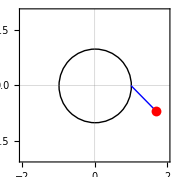

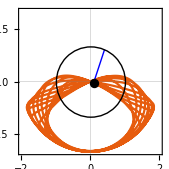
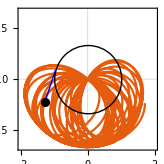

```mathematica
g:=9.8
l:=1(*Pendulum arm length*)
r:=1(*radius of disk*)
w:=-2(*Angular momentum of disk*)
tmax:=50(*time range*)
```

Piecewise[{{x[t]=, lSin[θ]+rCos[ϕ]}, {y[t]=, rSin[ϕ]-lCos[θ]}}]
ϕ=ωt
->Piecewise[{{x'[t]=, lθ' Cos[θ]-rωSin[ωt]}, {y'[t]=, rωCos[ωt]+lθ' Sin[θ]}}]
->T=1/2 m(x^(′^2)+y^(′^2))=1/2 m[l^2 θ^(′^2)+a^2 ω^2+2 rωlθ'+Sin[θ-ωt]]
U=mgy=mg[rSin[ϕ]-lCos[θ]]
L=T-U=1/2 m[l^2 θ^(′^2)+a^2 ω^2+2 rωlθ'+Sin[θ-ωt]]-mg[rSin[ϕ]-lCos[θ]]
(∂L)/(∂θ)-ⅆ/ⅆt(∂L)/(∂θ')=0

```mathematica
solv=Flatten[NDSolve[{θ''[t]==-g/l*Sin[θ[t]]+r*w^2/l Cos[θ[t]-w*t],θ[0]==π/4,θ'[0]==0},{θ[t]},{t,0,tmax}]]
θ[t_]:=Evaluate[θ[t]/.solv]
```

{θ[t]→InterpolatingFunction[…][t]}

```mathematica
y1[t_]:=r*Sin[w*t]
x1[t_]:=r*Cos[w*t]
x2[t_]:=x1[t]+l*Sin[θ[t]]
y2[t_]:=y1[t]-l*Cos[θ[t]]
```

```mathematica
Animate[Show[ParametricPlot[{x2[t1],y2[t1]},{t1,0,t},Background->White,PlotTheme->"Scientific",PlotRange->{{-2,2},{-2,2}}],Graphics[{Thick,Blue,Line[{{x1[t],y1[t]},{x2[t],y2[t]}}]}],Graphics[{Circle[{0,0},r]}],Graphics[{PointSize[0.04],Black,Point[{x2[t],y2[t]}]}]],{t,10^-10,tmax},AnimationRunning->False]
```